```mathematica
SetDirectory ["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/FREN/order3/PERF/1_fel_fqh/output_0.0001GPa"];
filesPERF={"volume_expansion","volume_expansion_relative","heat_capacity_isobaric","bulk_modulus_isothermal","enthalpy","entropy"};
dataPERF= Table[ReadList[filesPERF[[i]],Table[Number,{i,1,2}]],{i,1,Length[filesPERF]}];
```

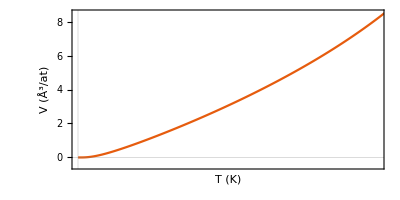

```mathematica
plotStyleVol={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{None,True},FrameLabel->{Style["T (K)",18,Opacity[0]],Style["V (Å^3/at)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->400,PlotRange->{{0,3000},{-0.5,8.5}}};
p1=ListLinePlot[dataPERF[[2]],plotStyleVol]
```

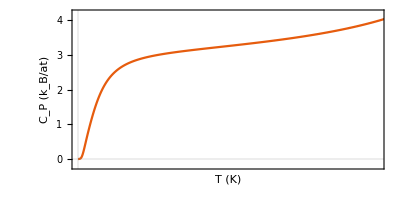

```mathematica
plotStyleHeat={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{None,True},FrameLabel->{Style["T (K)",18,Opacity[0]],Style["C_P (k_B/at)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->400,PlotRange->{{0,3000},{-0.2,4.2}}};
p2=ListLinePlot[dataPERF[[3]],plotStyleHeat]
```

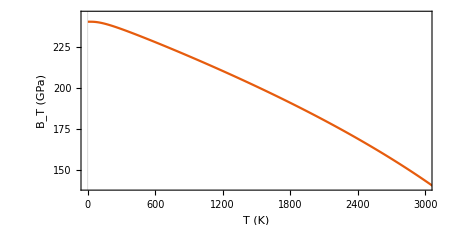

```mathematica
plotStyleBulk={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,True},FrameLabel->{Style["T (K)",18,Black],Style["B_T (GPa)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->450,PlotRange->{{0,3000},{140,245}}};
p3=ListLinePlot[dataPERF[[4]],plotStyleBulk]
```

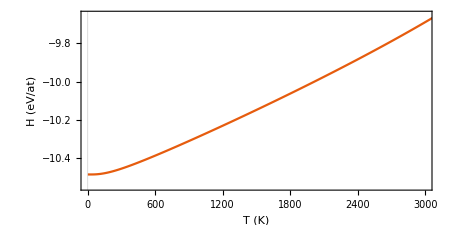

```mathematica
plotStyleEnthalpy={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,True},FrameLabel->{Style["T (K)",18,Black],Style["H (eV/at)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->450,PlotRange->{{0,3000},{-10.55,-9.65}}};
p4=ListLinePlot[Transpose@{Transpose[dataPERF[[5]]][[1]],Transpose[dataPERF[[5]]][[2]]*0.001},plotStyleEnthalpy]
```

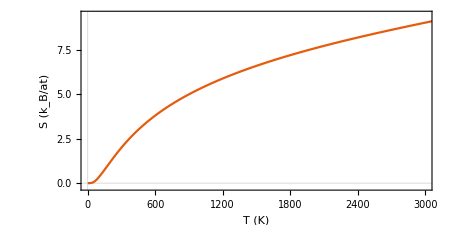

```mathematica
p5=plotStyleEnthalpy={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,True},FrameLabel->{Style["T (K)",18,Black],Style["S (k_B/at)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->450,PlotRange->{{0,3000},{-0.2,9.5}}};
ListLinePlot[dataPERF[[6]],plotStyleEnthalpy]
```

```mathematica
SetDirectory ["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/FREN/order3"];
filesFREN={"volume_expansion.2_fqh_fel_sizeFINITE.all","volume_expansion_relative.2_fqh_fel_sizeFINITE.all","heat_capacity_isobaric.2_fqh_fel_sizeFINITE.all","bulk_modulus_isothermal.2_fqh_fel_sizeFINITE.all","enthalpy.2_fqh_fel_sizeFINITE.all","entropy.2_fqh_fel_sizeFINITE.all"};
dataFREN= Table[ReadList[filesFREN[[i]],Table[Number,{i,1,6}]],{i,1,Length[filesFREN]}];
```

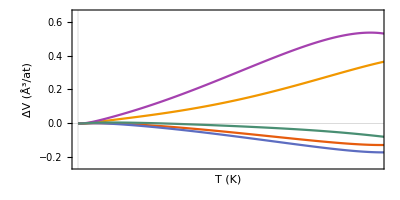

```mathematica
plotStyleVolf={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{None,True},FrameLabel->{Style["T (K)",18,Opacity[0]],Style["ΔV (Å^3/at)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->400,PlotRange->{{0,3000},{-0.25,0.65}}};
q1=ListLinePlot[Table[Transpose@{Transpose[dataFREN[[2]]][[1]],Transpose[dataFREN[[2]]][[1+i]]},{i,1,5}],plotStyleVolf]
```

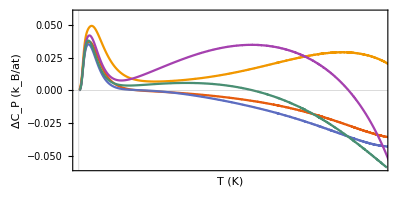

```mathematica
plotStyleHeatf={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{None,True},FrameLabel->{Style["T (K)",18,Opacity[0]],Style["ΔC_P (k_B/at)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->404,PlotRange->{{0,3000},{-0.059,0.059}}};
q2=ListLinePlot[Table[MovingAverage[Transpose@{Transpose[dataFREN[[3]]][[1]],Transpose[dataFREN[[3]]][[1+i]]},10],{i,1,5}],plotStyleHeatf]
```

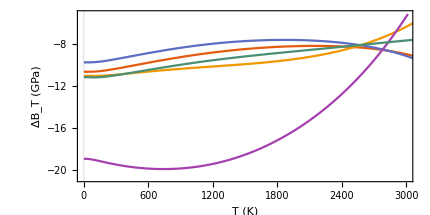

```mathematica
plotStyleBulk={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,True},FrameLabel->{Style["T (K)",18,Black],Style["ΔB_T (GPa) ",18,Black] "\n" },FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->430,PlotRange->{{0,3000},{-20.80,-5.20}}};
q3=ListLinePlot[Table[Transpose@{Transpose[dataFREN[[4]]][[1]],Transpose[dataFREN[[4]]][[1+i]]},{i,1,5}],plotStyleBulk]
```

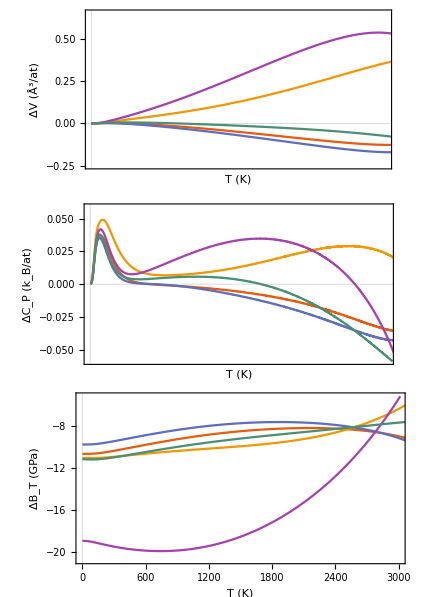

```mathematica
GraphicsGrid[Transpose@{{q1,q2,q3}},Spacings->-20]
```

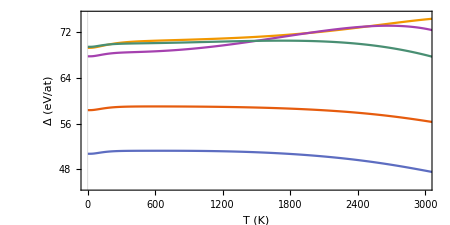

```mathematica
plotStyleEnthalpy={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,True},FrameLabel->{Style["T (K)",18,Black],Style["Δ (eV/at)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->450,PlotRange->{{0,3000},{45,75}}};
q4=ListLinePlot[Table[Transpose@{Transpose[dataFREN[[5]]][[1]],Transpose[dataFREN[[5]]][[1+i]]},{i,1,5}],plotStyleEnthalpy]
```

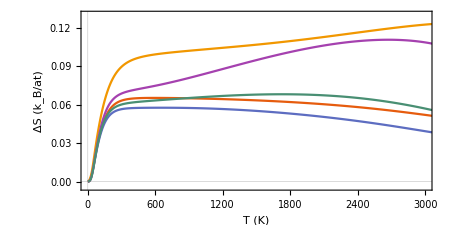

```mathematica
plotStyleEnthalpy={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,True},FrameLabel->{Style["T (K)",18,Black],Style["ΔS (k_B/at)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->450,PlotRange->{{0,3000},{-0.004,0.13}}};
q5=ListLinePlot[Table[Transpose@{Transpose[dataFREN[[6]]][[1]],Transpose[dataFREN[[6]]][[1+i]]},{i,1,5}],plotStyleEnthalpy]
```

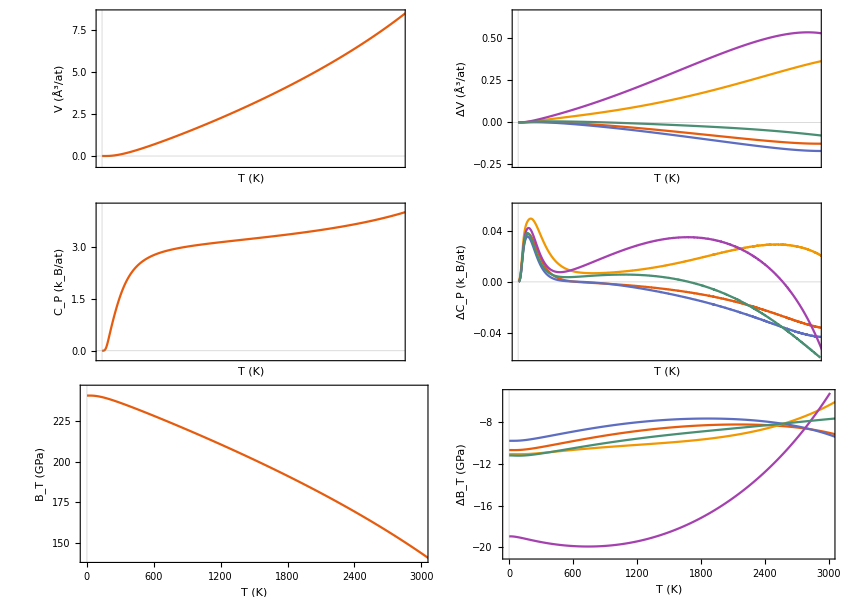

```mathematica
GraphicsGrid[Transpose@{{p1,p2,p3},{q1,q2,q3}},Spacings->-30]
```